```mathematica
SeedRandom[6203];
data=Table[Insert[AngleVector[1+{2,8}*RandomReal[]],RandomReal[],2],800];
```

```mathematica
ListPointPlot3D[data,BoxRatios->{1,1,1},PlotStyle->Directive[PointSize->Medium]]
```

-Graphics3D-

```mathematica
mdsmodel=DimensionReduction[data,Method-> "MultidimensionalScaling"]
```

DimensionReducerFunction[…]

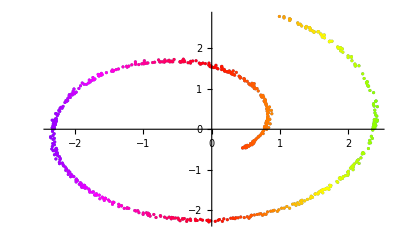

```mathematica
mdspts=mdsmodel[data];
ListPlot[Style[#,Hue[First[#]/10]]&/@ mdspts]
```

```mathematica
ListPointPlot3D[Style[#,Hue[First[mdsmodel[#]]/10]] & /@ data,PlotStyle->Directive[PointSize->Large],BoxRatios->{1,1,1}]
```

-Graphics3D-

#### Isomap method

```mathematica
isomapmodel=DimensionReduction[data,2,Method-> "Isomap"]
```

DimensionReducerFunction[…]

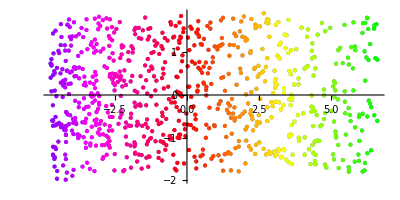

```mathematica
isomappts=isomapmodel[data];
ListPlot[Style[#,Hue[First[#]/20]] & /@ isomappts, AspectRatio->1/2, PlotStyle->Directive[PointSize->Small]]
```

Note what happens when we change the number of points

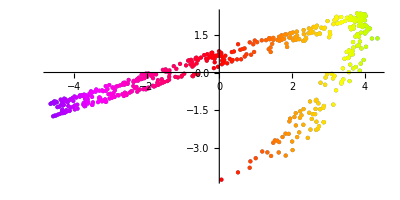

```mathematica
data1=Table[Insert[AngleVector[1+{2,8}*RandomReal[]],RandomReal[],2],500];
isomapmodel=DimensionReduction[data1,2,Method-> "Isomap"];
isomappts=isomapmodel[data1];
ListPlot[Style[#,Hue[First[#]/20]] & /@ isomappts, AspectRatio->1/2, PlotStyle->Directive[PointSize->Medium]]
```

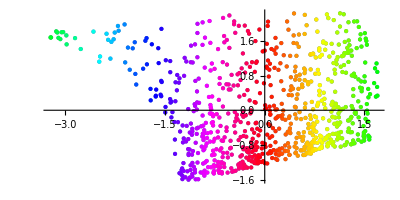

```mathematica
llemodel=DimensionReduction[data,2,Method-> "LLE"];
llepts=llemodel[data];
ListPlot[Style[#,Hue[First[#]/5]] & /@ llepts, AspectRatio->1/2, PlotStyle->Directive[PointSize->Medium]]
```

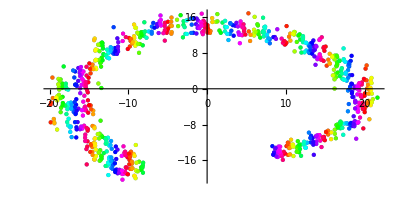

```mathematica
tsnemodel=DimensionReduction[data,2,Method-> {"TSNE","Perplexity"-> 50}];
tsnepts=tsnemodel[data];
ListPlot[Style[#,Hue[First[#]/5]] & /@ tsnepts, AspectRatio->1/2, PlotStyle->Directive[PointSize->Medium]]
```

```mathematica
flowers = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
reduced = DimensionReduce[flowers, 2, Method->{"TSNE", "LinearPrereduction"-> True}];
```

```mathematica
ListPlot[MapThread[Labeled[#1, #2]&, {reduced, flowers}]]
```

-Graphics-